# Vaje 8 - Podatkovna analiza z Mathematico

1. a) Z ukazom ‘Directory’ preveri delovno področje. Nato z uporabo ‘SetDirectory’ in ‘NotebookDirectory’ nastavi delovno področje na ustrezno mapo.

```mathematica
Directory []
```

C:\Users\si9164

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\si9164\Desktop\ROM\ROM-2025-26\Vaje 8

1. b) Z ukazom ‘Import’ uvozi tabelo iz datoteke ‘rezultati.xlsx’, v kateri se nahajajo rezultati pisnega izpita pri nekem predmetu. Podatke uvozi v formatu ‘Dataset’. Uvožena tabela naj ima označeno “glavo” (prvo vrstico - ukaz ‘HeaderLines’).  Tabelo shani v spremenljivko ‘podatki’.

```mathematica
podatki = First[Import["rezultati.xlsx", "Dataset", "HeaderLines" ->1]];
```

2. Sestavi naslednje funkcije:
 1.) Imena[podatki_], ki vrne seznam imen stolpcev (prva vrstica tabele). Uporabiš lahko funkcijo ‘Keys’.
 2.) Podatki[podatki_], ki vrne tabelo podatkov, t.j. podatke v vrsticah brez glave tabele. Uporabiš lahko funkcijo ‘Values’.
 3.) IndeksStolpca[podatki_, stolpec_], ki za dano ime stolpca vrne indeks stolpca. Npr. pri naši tabeli klic IndeksStolpca[podatki, “Ime”] vrne 2. Če stolpec s tem imenom ne obstaja, naj funkcija vrne Null (prazno). Poskusi uporabiti funkcijo ‘Position’, za definiranje lokalnih spremenljivk pa lahko uporabiš funkcijo ‘Module’.
 4.) Stolpec[podatki_, stolpec_], ki vrne podatke v stolpcu s podanim imenom stolpec. Seznam naj vsebuje samo podatke, ne pa tudi glave. Poskusi uporabiti funkcijo ‘Transpose’.
5.) PovprecjeTock[podatki_], ki izračuna povprečje doseženih točk. Uporabi funkcijo ‘Mean’.
6.) RazlicneVrednosti[podatki_, stolpec_], ki vrne seznam različnih vrednosti za stolpec. Koliko skupin testov so pisali? Namig: preveri, kaj naredi funkcija ‘Union’ na seznamih, v katerih se ponavaljajo vrednosti.
7.) Vrstica[podatki_, i_], ki vrne i-to vrstico v tabeli. Pazi: vrstice z glavo ne šteješ. Vrstica z indeksom 1 je prva naslednja vrstica po glavi, t.j. prva vrstica podatkov.

```mathematica
Imena[podatki_]:=Normal[First[Keys[podatki]]]
Imena[podatki]
```

{Priimek,Ime,Skupina,Točke}

```mathematica
Podatki[podatki_]:=Normal[Values[podatki]]
Normal[podatki]
```

{<|Priimek→Furlan,Ime→Luka,Skupina→A,Točke→93.|>,<|Priimek→Karakaš,Ime→Alenka,Skupina→A,Točke→94.|>,<|Priimek→Kočar,Ime→Petra,Skupina→B,Točke→44.|>,<|Priimek→Kofol,Ime→Andraž,Skupina→C,Točke→34.|>,<|Priimek→Kumar,Ime→Barbara,Skupina→B,Točke→67.|>,<|Priimek→Logar,Ime→Mateja,Skupina→A,Točke→42.|>,<|Priimek→Pance,Ime→Martin,Skupina→B,Točke→64.|>,<|Priimek→Pleterski,Ime→Vesna,Skupina→C,Točke→30.|>,<|Priimek→Trček,Ime→Valerija,Skupina→B,Točke→70.|>,<|Priimek→Virant,Ime→Primož,Skupina→C,Točke→58.|>,<|Priimek→Vesel,Ime→Polona,Skupina→C,Točke→66.|>,<|Priimek→Žveglič,Ime→Katarina,Skupina→A,Točke→46.|>,<|Priimek→Cvelbar,Ime→Janja,Skupina→B,Točke→39.|>,<|Priimek→Furlan,Ime→Aleš,Skupina→B,Točke→36.|>,<|Priimek→Iskra,Ime→Sabina,Skupina→A,Točke→77.|>,<|Priimek→Jerman,Ime→Katja,Skupina→B,Točke→100.|>,<|Priimek→Karničar,Ime→Jaka,Skupina→C,Točke→26.|>,<|Priimek→Korošec,Ime→Kristina,Skupina→B,Točke→86.|>,<|Priimek→Kržišnik,Ime→Grega,Skupina→B,Točke→90.|>,<|Priimek→Obrenović,Ime→Tatjana,Skupina→C,Točke→44.|>,<|Priimek→Puncer,Ime→Primož,Skupina→A,Točke→57.|>,<|Priimek→Ribnikar,Ime→Matjaž,Skupina→A,Točke→43.|>,<|Priimek→Štemberger,Ime→Igor,Skupina→B,Točke→85.|>,<|Priimek→Šubašič,Ime→Matej,Skupina→C,Točke→76.|>,<|Priimek→Tekavčič,Ime→Aleksander,Skupina→A,Točke→34.|>,<|Priimek→Tratnik,Ime→Mojca,Skupina→B,Točke→79.|>,<|Priimek→Smrekar,Ime→Andreja,Skupina→A,Točke→38.|>,<|Priimek→Bezek,Ime→Tomaž,Skupina→B,Točke→38.|>}

```mathematica
IndeksStolpca[podatki_,stolpec_]:=If[MemberQ[Imena[podatki], stolpec],
									Position[Imena[podatki],stolpec][[1]][[1]],
									Null]
IndeksStolpca[podatkiOcene, "Ocena"]
```

5

```mathematica
Stolpec[podatki_,stolpec_]:=Normal[Transpose[podatki][[stolpec]]]
Stolpec[podatki,"Točke"]
```

{93.,94.,44.,34.,67.,42.,64.,30.,70.,58.,66.,46.,39.,36.,77.,100.,26.,86.,90.,44.,57.,43.,85.,76.,34.,79.,38.,38.}

```mathematica
PovprecjeTock[podatki_]:=Mean[Stolpec[podatki,"Točke"]]
PovprecjeTock[podatki]
```

59.1429

```mathematica
RazlicneVrednosti[podatki_,stolpec_]:= Union[Stolpec[podatki,stolpec]]
RazlicneVrednosti[podatki,"Skupina"]
```

{A,B,C}

```mathematica
Vrstica[podatki_, i_]:= Normal[Podatki[podatki][[i]]]
Vrstica[podatki, 1]
```

{Furlan,Luka,A,93.}

3. Sestavi funkcijo OcenaZaMeje[{za6_, za7_, za8_, za9_, za10_}, tocke_], pri kateri so v prvem argumentu meje za ocene v številu točk, v drugem argumentu pa število točk, za katere
želimo izračunati oceno. Funkcijo napiši s pomočjo ustreznih stavkov ‘If’. Nato siesta funkcijo Ocene[podatki_, meje_], ki izračuna stolpec ocen za dane podatke in meje.

```mathematica
OcenaZaMeje[{za6_, za7_, za8_, za9_, za10_}, tocke_]:=If[tocke>=za10,10,
														If[tocke>=za9,9,
														If[tocke>=za8,8,
														If[tocke>=za7,7,
														If[tocke>=za6,6,0]]]]]
Ocene[podatki_, meje_]:=Table[OcenaZaMeje[meje,Stolpec[podatki,"Točke"][[i]]],{i,1,Length[podatki]}]
meje = {50,60,70,80,90};
ocene = Ocene[podatki,meje]
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

4. Sestavi funkcijo DodajStolpec[podatki_], ki obstoječi tabeli doda še en stolpec (oz . vrne novo tabelo z dodanim stolpcem) . Premisli, kako s pomočjo ‘Query’ dodaš stolpec tabeli.  Podatkom dodaj stolpec "Ocena" z ocenami in vse skupaj shrani v spremenljivko podatkiOcene. Novo tabelo shrani v Excelov zvezek ‘ocene.xlsx’ s pomočjo ukaza ‘Export’ .

```mathematica
DodajStolpec[podatki_]:=Query[All,<|#,"Ocena"->OcenaZaMeje[meje,#["Točke"]]|>&]@podatki
podatkiOcene = DodajStolpec[podatki];
Export["ocene.xlsx",podatkiOcene];
```

5. Preveri, kaj naredi funkcija ‘BinCount’ na seznamu ocen. Ali bi se dele rezultata te funkcije dalo uporabiti, da bi prešteli, koliko študentov je dobilo kakšno oceno(Da)? Namig : uporabiš lahko funkcije za delo s seznami kot so Rest, Drop, Take, ... Izračunaj porazdelitev ocen in jo shrani v spremenljivko ‘porazdelitevOcen’. To je seznam šestih vrednosti, pri čemer prva predstavlja število študentov z negativno oceno, druga število študentov z oceno 6, . . .

```mathematica
porazdelitevOcen = Drop[BinCounts[ocene,{0,11,1}],{2,6}]  (*dobi seznam "ocene" in ga spremeni v sseznam kjer je vsak element število pojavitev določenega števila  (to od 0 do vključno 10 pro inkrementu 1) in odstranimo vse
															prazne elemente (ničle)*)
```

{13,2,3,4,2,4}

```mathematica
test = {0, 1, 2,3,4,15,2}
```

{0,1,2,3,4,15,2}

```mathematica
{0,1,2,3,4,15,2}
```

{0,1,2,3,4,15,2}

```mathematica
Query[All,#*6&]@ test
```

{0,6,12,18,24}

```mathematica
BinCounts[test,2]
```

{0,2,3,1,0,0,0,0,1}

# Vaje 9 - Nadaljevanje

6. stolpčni diagram

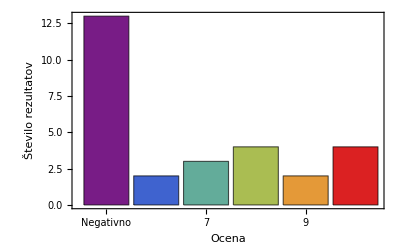

```mathematica
stolpcni = BarChart[porazdelitevOcen,ChartStyle->"Rainbow", ChartLabels->{"Negativno", 6, 7, 8, 9, 10},Frame->True,FrameLabel->{{"Število rezultatov", ""}, {"Ocena", "Ocene pri pisnem izpitu"}}]
```

```mathematica
Export["stolpcini.pdf",stolpcni];
```

7. tortni diagram

```mathematica
delezi = Table[N[100*porazdelitevOcen[[i]]/28], {i, 1, 6}];
```

```mathematica
zdruzi[napis_,delez_]:= StringJoin[napis,"(",ToString[DecimalForm[delez,{Infinity, 1}]],"%)"]
```

```mathematica
zdruzeniDeli = MapThread[zdruzi,{{"Negativno", "6", "7", "8", "9", "10"},delezi}];
```

```mathematica
PieChart3D[porazdelitevOcen, ChartLabels->zdruzeniDeli, PlotLabel->"Ocene pri pisanem izpitu"]
```

-Graphics3D-

8. funkcija UstrezaPogoju

```mathematica
v1 = Vrstica[podatkiOcene,2];
v2 = Vrstica[podatkiOcene,3];
```

```mathematica
UstrezaPogoju[podatki_,vrstica_,stolpec_,primerjava_,vrednost_]:= primerjava[vrstica[[IndeksStolpca[podatki,stolpec]]],vrednost]
```

```mathematica
UstrezaPogoju[podatkiOcene,v1,"Ocena",Equal,10]
UstrezaPogoju[podatkiOcene,v2,"Ocena",Equal,10]
```

True

False

9. funkcija IzberiVrstice NEDOKONČANO!!!!!!!

```mathematica
IzberiVrstice[podatki_,stolpec_,primerjava_,vrednost_]:= Module[{izbrano = Select[Podatki[podatki], UstrezaPogoju[podatki,#,stolpec,primerjava,vrednost]&]},

Table[izbrano[[i]][[]],{i,1,Length[izbrano]},{j,1,Length[izbrano[[i]]]} ]]
```

```mathematica
IzberiVrstice[podatkiOcene,"Ocena",Equal,10]
```

{{Priimek,Ime,Skupina,Točke,Ocena},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Jerman,Katja,B,100.,10},{Kržišnik,Grega,B,90.,10}}

10. PovprecjeZaSkupino

```mathematica
PovprecjeZaSkupino[podatki_,skupina_]:=Mean[Stolpec[Podatki[IzberiVrstice[podatki,"Skupina",Equal,skupina]],"Ocena"]]
```

```mathematica
PovprecjeZaSkupino[podatkiOcene,"A"]
```

Values::invrl: The argument {{Priimek,Ime,Skupina,Točke,Ocena},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Logar,Mateja,A,42.,0},{Žveglič,Katarina,A,46.,0},{Iskra,Sabina,A,77.,8},{Puncer,Primož,A,57.,6},{Ribnikar,Matjaž,A,43.,0},{Tekavčič,Aleksander,A,34.,0},{Smrekar,Andreja,A,38.,0}} is not a valid Association or a list of rules.

Part::pspec1: Part specification Ocena is not applicable.

Mean[Transpose[Values[{{Priimek,Ime,Skupina,Točke,Ocena},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Logar,Mateja,A,42.,0},{Žveglič,Katarina,A,46.,0},{Iskra,Sabina,A,77.,8},{Puncer,Primož,A,57.,6},{Ribnikar,Matjaž,A,43.,0},{Tekavčič,Aleksander,A,34.,0},{Smrekar,Andreja,A,38.,0}}]]⟦Ocena⟧]

```mathematica
Podatki[IzberiVrstice[podatkiOcene,"Skupina",Equal,"A"]]
```

Values::invrl: The argument {{Priimek,Ime,Skupina,Točke,Ocena},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Logar,Mateja,A,42.,0},{Žveglič,Katarina,A,46.,0},{Iskra,Sabina,A,77.,8},{Puncer,Primož,A,57.,6},{Ribnikar,Matjaž,A,43.,0},{Tekavčič,Aleksander,A,34.,0},{Smrekar,Andreja,A,38.,0}} is not a valid Association or a list of rules.

Values[{{Priimek,Ime,Skupina,Točke,Ocena},{Furlan,Luka,A,93.,10},{Karakaš,Alenka,A,94.,10},{Logar,Mateja,A,42.,0},{Žveglič,Katarina,A,46.,0},{Iskra,Sabina,A,77.,8},{Puncer,Primož,A,57.,6},{Ribnikar,Matjaž,A,43.,0},{Tekavčič,Aleksander,A,34.,0},{Smrekar,Andreja,A,38.,0}}]